```mathematica
fileName = FileNameJoin[{NotebookDirectory[],"optimizerHistory.json"}];
(*RadioButtonBar[
Dynamic[fileName],
{
FileNameJoin[{NotebookDirectory[],"optimizerHistory.json"}],
"~/Downloads/optimizerHistory.json"
},Appearance->"Vertical"]*)
```

```mathematica
raw=Import[fileName];

raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
(*Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]*)
```

```mathematica
runningBest = FoldList[Max,First[#],Rest[#]]&[raw[[All,"maximizeMe"]]];
```

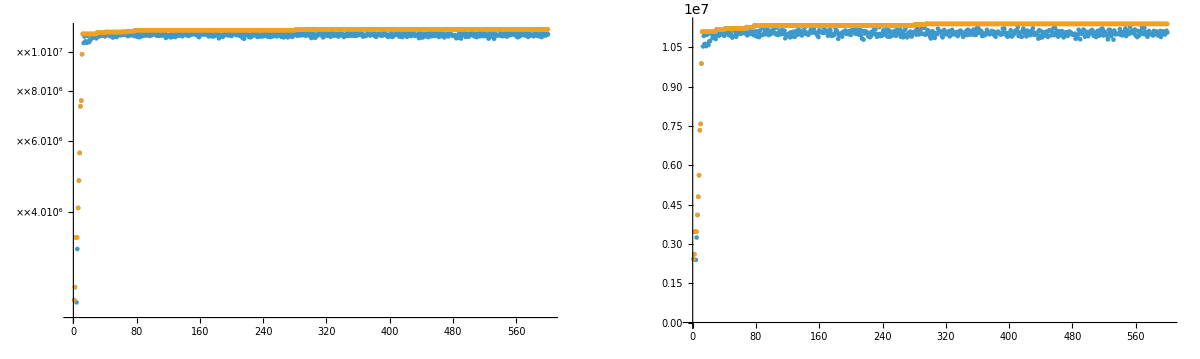

```mathematica
GraphicsGrid[{{
ListPlot[
{
#["maximizeMe"]&/@raw,
runningBest
},
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600,
ScalingFunctions->"SignedLog"
],
ListPlot[
{
#["maximizeMe"]&/@raw,
runningBest
},
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200]
```

### Live plot

```mathematica
(*Dynamic[livePlot]

makeLivePlot[]:=(
raw=Import[fileName];

raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];

livePlot = GraphicsGrid[{{
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600
],
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200];
)

task=CreateScheduledTask[makeLivePlot[],1]; (*Runs myFunction every 1 second*)
StartScheduledTask[task];*)
```

### Analyze

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]];
```

```mathematica
(*Format for yml*)
string = "";
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
];
string
```

S1ELkG : 46.7184266818
S2ELkG : -105.3191097073
S3ELkG : -360.0649312251
PDrive_median_x : -1.4262e-6
PDrive_median_y : -4.855e-7
PDrive_median_xp : -5.575e-7
PDrive_median_yp : -3.883e-7
PDrive_median_energy : 1.0000001600826114654e10
PDrive_sigmaSI90_x : 0.0000157797
PDrive_sigmaSI90_y : 8.0982e-6
PDrive_sigmaSI90_z : 0.0000126273
PDrive_sigmaSI90_xp : 0.0000371736
PDrive_sigmaSI90_yp : 0.000017469
PDrive_sigmaSI90_energy : 2.6583252019873384e7
PDrive_emitSI90_x : 9.227e-6
PDrive_emitSI90_y : 2.7291e-6
PDrive_norm_emit_x : 4.2356e-6
PDrive_norm_emit_y : 1.6251e-6
PDrive_charge_nC : 1.6
PDrive_BMAG_x : 1.2807740494
PDrive_BMAG_y : 1.2296546717
PDrive_sliced_BMAG_x : List(3.1985634149,1.574352785,1.1062469159,1.7348004957,4.9448016272)
PDrive_sliced_BMAG_y : List(1.5379429338,1.409957403,1.4261226972,1.2663375464,1.1343769849)
lostChargeFraction : 0.
errorTerm_lostChargeFraction : 0.
errorTerm_bunchSpacing : 0
errorTerm_transverseOffset : 0.
errorTerm_angleOffset : 0.
errorTerm_mainObjective : 0.
errorTerm_secondaryObjective : 7.901e-7
maximizeMe : 1.1391670744274497e7
inputBeamFilePathSuffix : "/beams/2024-10-22_Impact_OneBunch/2024-10-22_oneBunch.h5"
csrTF : False

```mathematica
(*Not tested to be robust... beware!*)
indepVarKeys = Keys[raw[[1]]][[1;;(Position[Keys[raw[[1]]],"PDrive_median_x"][[1,1]]-1)]]
```

{S1ELkG,S2ELkG,S3ELkG}

## Plot specific

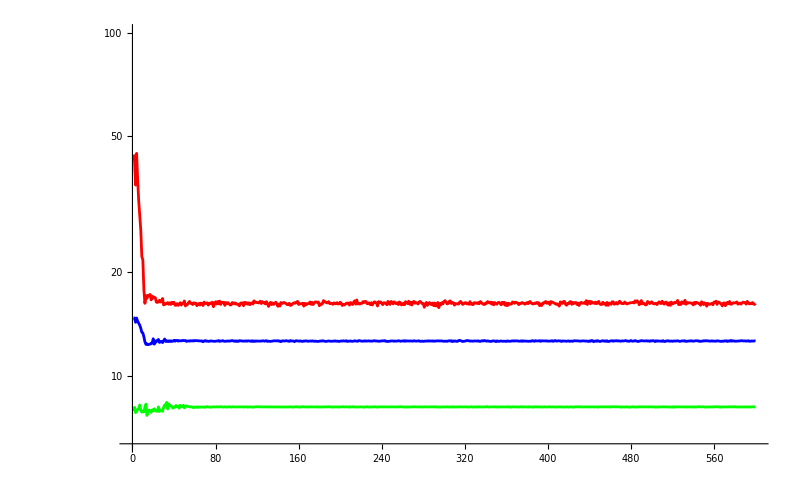

```mathematica
keys = {"PDrive_sigmaSI90_x","PDrive_sigmaSI90_y","PDrive_sigmaSI90_z","PWitness_sigmaSI90_x","PWitness_sigmaSI90_y","PWitness_sigmaSI90_z"};
ListLogPlot[
(10^6 raw[[All,#]]&/@keys)~Join~{(10^6 Max[#]&/@raw[[All,keys]])},
Joined->True,
ImageSize->800,
PlotStyle->{{Red},{Green},{Blue},{Red,Dashed},{Green,Dashed},{Blue,Dashed},{Black}},
InterpolationOrder->1,
PlotRange->{All,100}
]
(*ListPlot[
raw[[All,#]]&/@{"PWitness_sigmaSI90_x","PWitness_sigmaSI90_y","PWitness_sigmaSI90_z"},
Joined->True
]*)
```

```mathematica
If[MemberQ[Keys[raw[[1]]],"L1PhaseSet"],
ListDensityPlot[{
#["L1PhaseSet"],
#["L2PhaseSet"],
10^6#["PDrive_sigmaSI90_z"]
(*10^6 Max[{#["PDrive_sigmaSI90_z"],#["PWitness_sigmaSI90_z"]}]*)
}&/@raw,ImageSize->800,
ColorFunction->"Rainbow",InterpolationOrder->0,
PlotRange->{All,50},
(*PlotRange->{{-35,-21},{-50,-30},{All,50}},*)
Mesh->All,ColorFunction->"Rainbow",PlotLegends->Automatic,
FrameLabel->{"L1 Phase [°]","L2 Phase [°]"},PlotLabel->"Bunch length, SI90 [μm]",LabelStyle->20]
]
```

```mathematica
If[MemberQ[Keys[raw[[1]]],"L1PhaseSet"]&&MemberQ[Keys[raw[[1]]],"PWitness_sigmaSI90_z"],
ListDensityPlot[{
#["L1PhaseSet"],
#["L2PhaseSet"],
10^6 Max[{#["PDrive_sigmaSI90_z"],#["PWitness_sigmaSI90_z"]}]
}&/@raw,ImageSize->800,
ColorFunction->"Rainbow",InterpolationOrder->0,PlotRange->{All,50},Mesh->All,ColorFunction->"Rainbow",PlotLegends->Automatic]
]
```

```mathematica
If[MemberQ[Keys[raw[[1]]],"L1PhaseSet"],
ListDensityPlot[{
#["L1PhaseSet"],
#["L2PhaseSet"],
#["maximizeMe"]
}&/@raw,ImageSize->800,
ColorFunction->"Rainbow",
InterpolationOrder->0,
(*PlotRange->{1*^5,All},*)
PlotRange->{{-35,-21},{-50,-30},{1*^5,All}},
Mesh->All,
ColorFunction->"Rainbow",
PlotLegends->Automatic,
FrameLabel->{"L1 Phase [°]","L2 Phase [°]"},PlotLabel->"maximizeMe",LabelStyle->20]
]
```

```mathematica
If[MemberQ[Keys[raw[[1]]],"L1PhaseSet"],
toPlot = {
#["L1PhaseSet"],
#["L2PhaseSet"]
}&/@raw[[1;;-1;;10]];
colors = Table[ColorData["Rainbow"][Rescale[i,{1,Length[toPlot]}]],{i,Length[toPlot]}];

ListPlot[{#}&/@toPlot,
ImageSize->800,
FrameLabel->{"L1 Phase [°]","L2 Phase [°]"},
LabelStyle->20,
Frame->True,
PlotStyle->colors,
PlotLabel->"Iteration number = color; later iterations are more red",
PlotMarkers->{Graphics[Disk[]],0.01}
]
]
```

```mathematica
(*Show[
ListContourPlot3D[
{
#["S1ELkG"],
#["S2ELkG"],
#["S3ELkG"],
(10^6#["PDrive_sigmaSI90_z"])
}&/@raw,
PlotLegends->Automatic,
ImageSize->800,
SphericalRegion->True,
Contours->{4,4.9,5,5.1,6}
],
ListPointPlot3D[
{
#["S1ELkG"],
#["S2ELkG"],
#["S3ELkG"]
}&/@raw
]
]*)
```

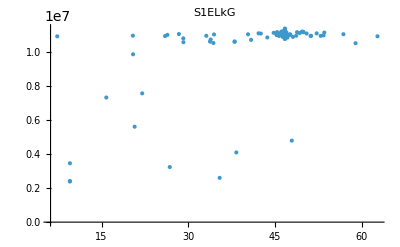
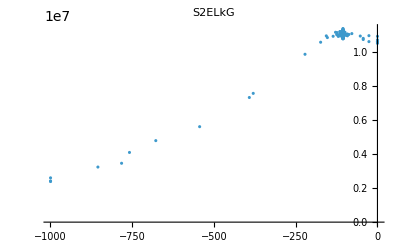
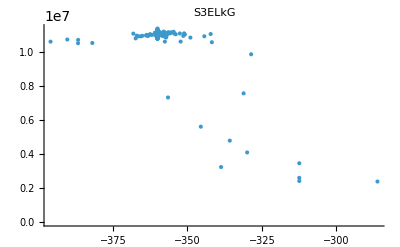
-Graphics- | -Graphics- | -Graphics- | 0

```mathematica
imgArr=ParallelTable[
ListPlot[
{#[key],#["maximizeMe"]}&/@raw,
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All
],
{key,indepVarKeys}
];

displayCols = 4;
Grid[
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
],
Frame->All
]
```

## Plot all

```mathematica
(*This block can get really slow for large numbers of simulations; pare down number of points to plot*)
shotCount = Length[raw[[All,1]]];
indicesToPlot = DeleteDuplicates[Round[Range[1,shotCount,shotCount/1000]]];
```

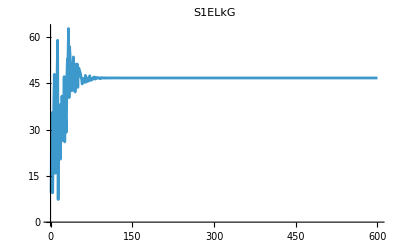
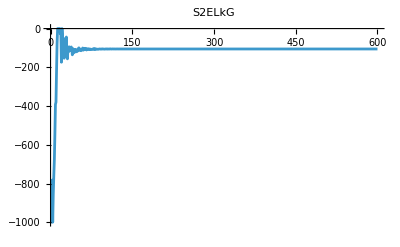
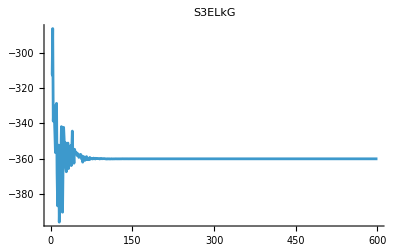
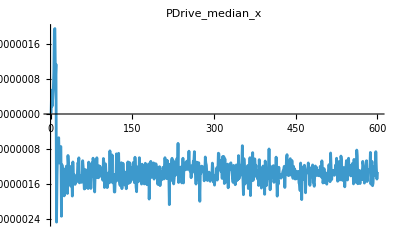
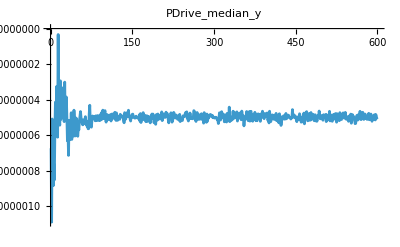
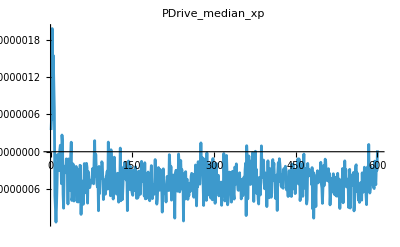
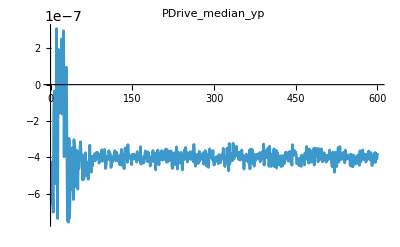
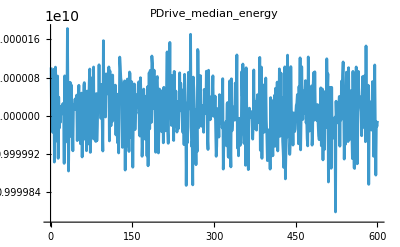
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | 0 | 0 | 0

```mathematica
imgArr=ParallelTable[
ListPlot[
raw[[indicesToPlot,key]],
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All,
Joined->True
],
{key,Keys[raw[[1]]]}
];

displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```

## Estimate maximizeMe asymptote

There’s no reason at all to think this is valid

```mathematica
(*runningBest = #["maximizeMe"]&/@raw;*)
```

```mathematica
Button["Calculate",

expr = a * Tanh[b ii]+c;
nlm=NonlinearModelFit[
Transpose[{Range[Length[runningBest]],runningBest}],
expr,
{
{a,Max[runningBest]},
{b,1/Length[runningBest]},
{c,Min[runningBest]}
},
ii,
Method->"NMinimize"
];

meanPredictionBands = nlm["MeanPredictionBands"];
singlePredictionBands = nlm["SinglePredictionBands"];
plotMe ={nlm["BestFit"]}~Join~meanPredictionBands~Join~singlePredictionBands;

img = Show[
ListPlot[
Transpose[{Range[Length[runningBest]],runningBest}],
PlotRange->{{0,Length[runningBest]*1.5},{0, Max[runningBest]*1.5}},
ImageSize->800
],

Plot[
plotMe,
{ii,0,Length[runningBest]*1.5},
PlotStyle->{{Opacity[0.5],Black},{Opacity[0.5],Red},{Opacity[0.5],Red},{Opacity[0.5],Green},{Opacity[0.5],Green}},
PlotRange->All
]

];

Print[
"Estimated limits: ",
Sort[
Limit[#,ii->Infinity]&/@plotMe
]
];
Print[img];
]
```

Calculate

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"QA10361kG","QA10371kG","QE10425kG","QE10441kG","QE10511kG","QE10525kG","L0BPhaseSet","L1PhaseSet","L2PhaseSet","L3PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","S1EL_xOffset","S1EL_yOffset","S2EL_xOffset","S2EL_yOffset","S2ER_xOffset","S2ER_yOffset","S1ER_xOffset","S1ER_yOffset","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG", "XC1FFkG","XC3FFkG","YC1FFkG","YC2FFkG"}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{S1ELkG,S2ELkG,S3ELkG}

```mathematica
fitVar = "PDrive_twiss_beta_x"
(*fitVar = "bunchSpacing"*)
```

PDrive_twiss_beta_x

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

LinearModelFit[{{9.53543,-998.886,-312.457,Missing[KeyAbsent,PDrive_twiss_beta_x]},{35.4354,-998.886,-312.457,Missing[KeyAbsent,PDrive_twiss_beta_x]},{9.53543,-781.826,-312.457,Missing[KeyAbsent,PDrive_twiss_beta_x]},{9.53543,-998.886,-286.207,Missing[KeyAbsent,PDrive_twiss_beta_x]},{26.8021,-854.179,-338.707,Missing[KeyAbsent,PDrive_twiss_beta_x]},{38.3132,-757.708,-329.957,Missing[KeyAbsent,PDrive_twiss_beta_x]},{47.9058,-677.315,-335.791,Missing[KeyAbsent,PDrive_twiss_beta_x]},{20.7268,-543.328,-345.513,Missing[KeyAbsent,PDrive_twiss_beta_x]},{15.8239,-391.475,-356.532,Missing[KeyAbsent,PDrive_twiss_beta_x]},{22.0413,-379.565,-331.146,Missing[KeyAbsent,PDrive_twiss_beta_x]},{20.4544,-221.36,-328.625,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.5873,-78.2748,-368.174,Missing[KeyAbsent,PDrive_twiss_beta_x]},{58.9379,0.,-386.746,Missing[KeyAbsent,PDrive_twiss_beta_x]},{7.33795,0.,-366.43,Missing[KeyAbsent,PDrive_twiss_beta_x]},{33.7625,0.,-352.288,Missing[KeyAbsent,PDrive_twiss_beta_x]},{38.0041,0.,-395.969,Missing[KeyAbsent,PDrive_twiss_beta_x]},{34.3479,0.,-381.939,Missing[KeyAbsent,PDrive_twiss_beta_x]},{20.4211,-26.0916,-367.011,Missing[KeyAbsent,PDrive_twiss_beta_x]},{38.0375,-26.0916,-357.583,Missing[KeyAbsent,PDrive_twiss_beta_x]},{29.1654,-173.665,-341.808,Missing[KeyAbsent,PDrive_twiss_beta_x]},{40.8652,0.,-386.704,Missing[KeyAbsent,PDrive_twiss_beta_x]},{33.8782,-43.486,-390.343,Missing[KeyAbsent,PDrive_twiss_beta_x]},{26.3926,-98.5682,-363.648,Missing[KeyAbsent,PDrive_twiss_beta_x]},{28.389,-91.8038,-342.212,Missing[KeyAbsent,PDrive_twiss_beta_x]},{47.1582,-153.006,-349.012,Missing[KeyAbsent,PDrive_twiss_beta_x]},{25.9913,-52.5321,-363.261,Missing[KeyAbsent,PDrive_twiss_beta_x]},{34.4551,-87.2941,-350.866,Missing[KeyAbsent,PDrive_twiss_beta_x]},{33.1241,-91.8038,-365.157,Missing[KeyAbsent,PDrive_twiss_beta_x]},{29.1431,-43.486,-367.399,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.9679,-128.096,-355.399,Missing[KeyAbsent,PDrive_twiss_beta_x]},{52.9095,-156.299,-351.399,Missing[KeyAbsent,PDrive_twiss_beta_x]},{52.2161,-103.973,-351.136,Missing[KeyAbsent,PDrive_twiss_beta_x]},{62.7257,-119.601,-365.607,Missing[KeyAbsent,PDrive_twiss_beta_x]},{40.3448,-94.0248,-353.937,Missing[KeyAbsent,PDrive_twiss_beta_x]},{56.836,-112.871,-362.536,Missing[KeyAbsent,PDrive_twiss_beta_x]},{53.4004,-108.944,-360.745,Missing[KeyAbsent,PDrive_twiss_beta_x]},{50.4667,-112.014,-352.557,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7142,-94.8818,-363.916,Missing[KeyAbsent,PDrive_twiss_beta_x]},{42.5525,-105.382,-354.425,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.6106,-135.446,-344.338,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.6926,-103.333,-359.837,Missing[KeyAbsent,PDrive_twiss_beta_x]},{53.5323,-123.58,-357.438,Missing[KeyAbsent,PDrive_twiss_beta_x]},{47.6618,-124.658,-362.559,Missing[KeyAbsent,PDrive_twiss_beta_x]},{49.8823,-114.648,-354.641,Missing[KeyAbsent,PDrive_twiss_beta_x]},{42.163,-107.138,-355.814,Missing[KeyAbsent,PDrive_twiss_beta_x]},{51.1637,-120.154,-357.1,Missing[KeyAbsent,PDrive_twiss_beta_x]},{48.8191,-110.876,-356.373,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.8761,-119.841,-356.879,Missing[KeyAbsent,PDrive_twiss_beta_x]},{51.2524,-116.831,-358.238,Missing[KeyAbsent,PDrive_twiss_beta_x]},{43.6728,-105.87,-357.155,Missing[KeyAbsent,PDrive_twiss_beta_x]},{49.6733,-114.547,-358.012,Missing[KeyAbsent,PDrive_twiss_beta_x]},{49.9139,-99.3292,-359.27,Missing[KeyAbsent,PDrive_twiss_beta_x]},{49.281,-103.603,-358.772,Missing[KeyAbsent,PDrive_twiss_beta_x]},{48.6797,-110.809,-358.621,Missing[KeyAbsent,PDrive_twiss_beta_x]},{48.1103,-108.362,-357.528,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.815,-114.338,-357.865,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.6813,-110.625,-360.021,Missing[KeyAbsent,PDrive_twiss_beta_x]},{44.7795,-108.055,-359.861,Missing[KeyAbsent,PDrive_twiss_beta_x]},{45.2873,-100.337,-361.948,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.4967,-111.421,-358.715,Missing[KeyAbsent,PDrive_twiss_beta_x]},{45.2979,-104.581,-358.922,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.3931,-109.366,-359.792,Missing[KeyAbsent,PDrive_twiss_beta_x]},{45.4134,-102.414,-360.945,Missing[KeyAbsent,PDrive_twiss_beta_x]},{47.5532,-102.02,-360.521,Missing[KeyAbsent,PDrive_twiss_beta_x]},{45.3573,-106.798,-359.999,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.8819,-110.583,-358.807,Missing[KeyAbsent,PDrive_twiss_beta_x]},{45.7193,-104.116,-360.499,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.5928,-105.344,-359.822,Missing[KeyAbsent,PDrive_twiss_beta_x]},{45.7026,-107.654,-359.93,Missing[KeyAbsent,PDrive_twiss_beta_x]},{45.74,-104.731,-360.56,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7813,-105.307,-360.186,Missing[KeyAbsent,PDrive_twiss_beta_x]},{47.4381,-108.613,-359.306,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.0937,-105.54,-360.299,Missing[KeyAbsent,PDrive_twiss_beta_x]},{45.9384,-108.193,-359.756,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.114,-107.592,-359.845,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.4596,-108.025,-359.802,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.2601,-105.475,-360.14,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.9205,-106.984,-359.652,Missing[KeyAbsent,PDrive_twiss_beta_x]},{47.0281,-103.739,-359.891,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.5781,-107.132,-359.82,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.339,-104.879,-360.153,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7993,-106.546,-359.757,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.6346,-105.335,-359.903,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.6249,-106.528,-359.902,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.8531,-106.429,-359.79,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.8296,-106.849,-359.935,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.789,-106.533,-359.928,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.6753,-105.651,-359.91,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.4926,-105.236,-360.128,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.5677,-105.485,-360.057,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.778,-106.181,-359.86,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.6115,-105.63,-360.016,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7342,-106.036,-359.901,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7937,-104.809,-360.015,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7585,-105.167,-359.992,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.6897,-105.54,-359.961,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7289,-105.797,-359.956,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.656,-106.125,-359.956,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7126,-105.954,-360.023,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7839,-105.255,-360.073,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7477,-105.222,-360.152,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.6686,-105.742,-360.087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7105,-104.901,-360.179,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7122,-105.734,-360.056,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.6852,-105.601,-360.08,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.738,-105.254,-360.123,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7146,-105.742,-360.037,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7132,-105.04,-360.141,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7612,-104.808,-360.14,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.701,-105.436,-360.092,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7251,-105.632,-360.046,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7157,-105.164,-360.121,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.747,-105.056,-360.114,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7106,-105.356,-360.097,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7314,-105.276,-360.103,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7166,-105.216,-360.102,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7068,-105.397,-360.083,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7212,-105.446,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7203,-105.398,-360.073,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7399,-105.265,-360.078,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.733,-105.292,-360.079,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.735,-105.194,-360.092,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7233,-105.355,-360.077,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7158,-105.341,-360.085,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7294,-105.303,-360.08,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7271,-105.29,-360.091,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7217,-105.343,-360.073,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7282,-105.301,-360.074,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7167,-105.334,-360.078,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7107,-105.374,-360.053,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7173,-105.357,-360.049,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7093,-105.357,-360.039,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7191,-105.346,-360.066,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7149,-105.336,-360.073,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7168,-105.353,-360.054,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7154,-105.34,-360.068,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7165,-105.35,-360.057,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7133,-105.356,-360.057,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7189,-105.337,-360.066,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7173,-105.341,-360.058,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7231,-105.309,-360.068,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.723,-105.302,-360.075,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.333,-360.061,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7187,-105.331,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7216,-105.313,-360.067,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7177,-105.334,-360.06,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.715,-105.343,-360.06,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7154,-105.333,-360.058,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7148,-105.33,-360.062,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7174,-105.311,-360.063,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7169,-105.318,-360.062,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.719,-105.317,-360.062,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7208,-105.303,-360.068,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7165,-105.327,-360.06,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7188,-105.318,-360.063,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7174,-105.318,-360.063,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7164,-105.329,-360.06,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.72,-105.308,-360.067,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7171,-105.324,-360.062,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7165,-105.323,-360.064,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7173,-105.326,-360.064,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7173,-105.325,-360.064,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7176,-105.323,-360.063,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7172,-105.322,-360.064,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7178,-105.319,-360.064,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7177,-105.324,-360.064,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.718,-105.321,-360.066,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7179,-105.321,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7177,-105.322,-360.063,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7178,-105.321,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7176,-105.321,-360.064,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7179,-105.322,-360.064,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7181,-105.32,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7181,-105.318,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7181,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7182,-105.32,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7179,-105.32,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7181,-105.321,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7181,-105.32,-360.064,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7182,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7186,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7186,-105.32,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7182,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7182,-105.32,-360.064,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7182,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7186,-105.318,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7183,-105.318,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7182,-105.32,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.32,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7187,-105.318,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7183,-105.32,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7186,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7183,-105.32,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.318,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]}},{S1ELkG,S2ELkG,S3ELkG},{S1ELkG,S2ELkG,S3ELkG}]

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

-Graphics-

```mathematica
lm["ANOVATable"]
```

LinearModelFit[{{9.53543,-998.886,-312.457,Missing[KeyAbsent,PDrive_twiss_beta_x]},{35.4354,-998.886,-312.457,Missing[KeyAbsent,PDrive_twiss_beta_x]},{9.53543,-781.826,-312.457,Missing[KeyAbsent,PDrive_twiss_beta_x]},{9.53543,-998.886,-286.207,Missing[KeyAbsent,PDrive_twiss_beta_x]},{26.8021,-854.179,-338.707,Missing[KeyAbsent,PDrive_twiss_beta_x]},{38.3132,-757.708,-329.957,Missing[KeyAbsent,PDrive_twiss_beta_x]},{47.9058,-677.315,-335.791,Missing[KeyAbsent,PDrive_twiss_beta_x]},{20.7268,-543.328,-345.513,Missing[KeyAbsent,PDrive_twiss_beta_x]},{15.8239,-391.475,-356.532,Missing[KeyAbsent,PDrive_twiss_beta_x]},{22.0413,-379.565,-331.146,Missing[KeyAbsent,PDrive_twiss_beta_x]},{20.4544,-221.36,-328.625,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.5873,-78.2748,-368.174,Missing[KeyAbsent,PDrive_twiss_beta_x]},{58.9379,0.,-386.746,Missing[KeyAbsent,PDrive_twiss_beta_x]},{7.33795,0.,-366.43,Missing[KeyAbsent,PDrive_twiss_beta_x]},{33.7625,0.,-352.288,Missing[KeyAbsent,PDrive_twiss_beta_x]},{38.0041,0.,-395.969,Missing[KeyAbsent,PDrive_twiss_beta_x]},{34.3479,0.,-381.939,Missing[KeyAbsent,PDrive_twiss_beta_x]},{20.4211,-26.0916,-367.011,Missing[KeyAbsent,PDrive_twiss_beta_x]},{38.0375,-26.0916,-357.583,Missing[KeyAbsent,PDrive_twiss_beta_x]},{29.1654,-173.665,-341.808,Missing[KeyAbsent,PDrive_twiss_beta_x]},{40.8652,0.,-386.704,Missing[KeyAbsent,PDrive_twiss_beta_x]},{33.8782,-43.486,-390.343,Missing[KeyAbsent,PDrive_twiss_beta_x]},{26.3926,-98.5682,-363.648,Missing[KeyAbsent,PDrive_twiss_beta_x]},{28.389,-91.8038,-342.212,Missing[KeyAbsent,PDrive_twiss_beta_x]},{47.1582,-153.006,-349.012,Missing[KeyAbsent,PDrive_twiss_beta_x]},{25.9913,-52.5321,-363.261,Missing[KeyAbsent,PDrive_twiss_beta_x]},{34.4551,-87.2941,-350.866,Missing[KeyAbsent,PDrive_twiss_beta_x]},{33.1241,-91.8038,-365.157,Missing[KeyAbsent,PDrive_twiss_beta_x]},{29.1431,-43.486,-367.399,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.9679,-128.096,-355.399,Missing[KeyAbsent,PDrive_twiss_beta_x]},{52.9095,-156.299,-351.399,Missing[KeyAbsent,PDrive_twiss_beta_x]},{52.2161,-103.973,-351.136,Missing[KeyAbsent,PDrive_twiss_beta_x]},{62.7257,-119.601,-365.607,Missing[KeyAbsent,PDrive_twiss_beta_x]},{40.3448,-94.0248,-353.937,Missing[KeyAbsent,PDrive_twiss_beta_x]},{56.836,-112.871,-362.536,Missing[KeyAbsent,PDrive_twiss_beta_x]},{53.4004,-108.944,-360.745,Missing[KeyAbsent,PDrive_twiss_beta_x]},{50.4667,-112.014,-352.557,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7142,-94.8818,-363.916,Missing[KeyAbsent,PDrive_twiss_beta_x]},{42.5525,-105.382,-354.425,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.6106,-135.446,-344.338,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.6926,-103.333,-359.837,Missing[KeyAbsent,PDrive_twiss_beta_x]},{53.5323,-123.58,-357.438,Missing[KeyAbsent,PDrive_twiss_beta_x]},{47.6618,-124.658,-362.559,Missing[KeyAbsent,PDrive_twiss_beta_x]},{49.8823,-114.648,-354.641,Missing[KeyAbsent,PDrive_twiss_beta_x]},{42.163,-107.138,-355.814,Missing[KeyAbsent,PDrive_twiss_beta_x]},{51.1637,-120.154,-357.1,Missing[KeyAbsent,PDrive_twiss_beta_x]},{48.8191,-110.876,-356.373,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.8761,-119.841,-356.879,Missing[KeyAbsent,PDrive_twiss_beta_x]},{51.2524,-116.831,-358.238,Missing[KeyAbsent,PDrive_twiss_beta_x]},{43.6728,-105.87,-357.155,Missing[KeyAbsent,PDrive_twiss_beta_x]},{49.6733,-114.547,-358.012,Missing[KeyAbsent,PDrive_twiss_beta_x]},{49.9139,-99.3292,-359.27,Missing[KeyAbsent,PDrive_twiss_beta_x]},{49.281,-103.603,-358.772,Missing[KeyAbsent,PDrive_twiss_beta_x]},{48.6797,-110.809,-358.621,Missing[KeyAbsent,PDrive_twiss_beta_x]},{48.1103,-108.362,-357.528,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.815,-114.338,-357.865,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.6813,-110.625,-360.021,Missing[KeyAbsent,PDrive_twiss_beta_x]},{44.7795,-108.055,-359.861,Missing[KeyAbsent,PDrive_twiss_beta_x]},{45.2873,-100.337,-361.948,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.4967,-111.421,-358.715,Missing[KeyAbsent,PDrive_twiss_beta_x]},{45.2979,-104.581,-358.922,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.3931,-109.366,-359.792,Missing[KeyAbsent,PDrive_twiss_beta_x]},{45.4134,-102.414,-360.945,Missing[KeyAbsent,PDrive_twiss_beta_x]},{47.5532,-102.02,-360.521,Missing[KeyAbsent,PDrive_twiss_beta_x]},{45.3573,-106.798,-359.999,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.8819,-110.583,-358.807,Missing[KeyAbsent,PDrive_twiss_beta_x]},{45.7193,-104.116,-360.499,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.5928,-105.344,-359.822,Missing[KeyAbsent,PDrive_twiss_beta_x]},{45.7026,-107.654,-359.93,Missing[KeyAbsent,PDrive_twiss_beta_x]},{45.74,-104.731,-360.56,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7813,-105.307,-360.186,Missing[KeyAbsent,PDrive_twiss_beta_x]},{47.4381,-108.613,-359.306,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.0937,-105.54,-360.299,Missing[KeyAbsent,PDrive_twiss_beta_x]},{45.9384,-108.193,-359.756,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.114,-107.592,-359.845,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.4596,-108.025,-359.802,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.2601,-105.475,-360.14,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.9205,-106.984,-359.652,Missing[KeyAbsent,PDrive_twiss_beta_x]},{47.0281,-103.739,-359.891,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.5781,-107.132,-359.82,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.339,-104.879,-360.153,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7993,-106.546,-359.757,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.6346,-105.335,-359.903,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.6249,-106.528,-359.902,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.8531,-106.429,-359.79,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.8296,-106.849,-359.935,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.789,-106.533,-359.928,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.6753,-105.651,-359.91,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.4926,-105.236,-360.128,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.5677,-105.485,-360.057,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.778,-106.181,-359.86,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.6115,-105.63,-360.016,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7342,-106.036,-359.901,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7937,-104.809,-360.015,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7585,-105.167,-359.992,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.6897,-105.54,-359.961,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7289,-105.797,-359.956,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.656,-106.125,-359.956,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7126,-105.954,-360.023,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7839,-105.255,-360.073,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7477,-105.222,-360.152,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.6686,-105.742,-360.087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7105,-104.901,-360.179,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7122,-105.734,-360.056,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.6852,-105.601,-360.08,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.738,-105.254,-360.123,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7146,-105.742,-360.037,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7132,-105.04,-360.141,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7612,-104.808,-360.14,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.701,-105.436,-360.092,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7251,-105.632,-360.046,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7157,-105.164,-360.121,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.747,-105.056,-360.114,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7106,-105.356,-360.097,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7314,-105.276,-360.103,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7166,-105.216,-360.102,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7068,-105.397,-360.083,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7212,-105.446,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7203,-105.398,-360.073,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7399,-105.265,-360.078,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.733,-105.292,-360.079,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.735,-105.194,-360.092,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7233,-105.355,-360.077,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7158,-105.341,-360.085,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7294,-105.303,-360.08,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7271,-105.29,-360.091,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7217,-105.343,-360.073,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7282,-105.301,-360.074,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7167,-105.334,-360.078,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7107,-105.374,-360.053,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7173,-105.357,-360.049,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7093,-105.357,-360.039,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7191,-105.346,-360.066,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7149,-105.336,-360.073,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7168,-105.353,-360.054,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7154,-105.34,-360.068,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7165,-105.35,-360.057,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7133,-105.356,-360.057,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7189,-105.337,-360.066,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7173,-105.341,-360.058,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7231,-105.309,-360.068,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.723,-105.302,-360.075,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.333,-360.061,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7187,-105.331,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7216,-105.313,-360.067,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7177,-105.334,-360.06,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.715,-105.343,-360.06,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7154,-105.333,-360.058,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7148,-105.33,-360.062,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7174,-105.311,-360.063,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7169,-105.318,-360.062,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.719,-105.317,-360.062,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7208,-105.303,-360.068,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7165,-105.327,-360.06,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7188,-105.318,-360.063,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7174,-105.318,-360.063,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7164,-105.329,-360.06,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.72,-105.308,-360.067,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7171,-105.324,-360.062,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7165,-105.323,-360.064,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7173,-105.326,-360.064,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7173,-105.325,-360.064,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7176,-105.323,-360.063,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7172,-105.322,-360.064,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7178,-105.319,-360.064,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7177,-105.324,-360.064,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.718,-105.321,-360.066,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7179,-105.321,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7177,-105.322,-360.063,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7178,-105.321,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7176,-105.321,-360.064,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7179,-105.322,-360.064,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7181,-105.32,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7181,-105.318,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7181,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7182,-105.32,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7179,-105.32,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7181,-105.321,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7181,-105.32,-360.064,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7182,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7186,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7186,-105.32,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7182,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7182,-105.32,-360.064,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7182,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7186,-105.318,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7183,-105.318,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7182,-105.32,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.32,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7187,-105.318,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7183,-105.32,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7186,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7183,-105.32,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.318,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7185,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]},{46.7184,-105.319,-360.065,Missing[KeyAbsent,PDrive_twiss_beta_x]}},{S1ELkG,S2ELkG,S3ELkG},{S1ELkG,S2ELkG,S3ELkG}][ANOVATable]

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
(*
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];*)
```

```mathematica
(*displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm*)
```

## Parse JSON strings to assoc

```mathematica
(*This is a stupid trick, but ensures numbers in scientific notation are interpreted correctly: https://mathematica.stackexchange.com/questions/15051/reading-in-scientific-notation-from-c-to-mathematica*)
stringToNumber[string_]:=ImportString[string,"Table"][[1,1]]
```

```mathematica
jsonTextToAssoc[string_]:=(
stringParts = StringSplit[StringDelete[#,WhitespaceCharacter],":"]&/@StringSplit[string,"\n"];
Association[#[[1]]->stringToNumber[#[[2]]]&/@stringParts]
)
```

```mathematica
tmp="L0BPhaseSet : -1.7210344516
L1PhaseSet : -20.3120443443
L2PhaseSet : -38.6737055166
L3PhaseSet : -1.4632882388
S1EL_xOffset : 0.0003852549
S1EL_yOffset : -0.0002411137
S2EL_xOffset : -0.0014178669
S2EL_yOffset : 0.0000111705
S2ER_xOffset : -0.002238162
S2ER_yOffset : -0.0006759962
S1ER_xOffset : 0.0010071369
S1ER_yOffset : 0.0003984557
XC1FFkG : 0.2064553639
XC3FFkG : -0.089916372
YC1FFkG : -0.0022311951
YC2FFkG : -0.0085115845";
```

```mathematica
priorSettings = jsonTextToAssoc[tmp]
```

<|L0BPhaseSet→-1.72103,L1PhaseSet→-20.312,L2PhaseSet→-38.6737,L3PhaseSet→-1.46329,S1EL_xOffset→0.000385255,S1EL_yOffset→-0.000241114,S2EL_xOffset→-0.00141787,S2EL_yOffset→0.0000111705,S2ER_xOffset→-0.00223816,S2ER_yOffset→-0.000675996,S1ER_xOffset→0.00100714,S1ER_yOffset→0.000398456,XC1FFkG→0.206455,XC3FFkG→-0.0899164,YC1FFkG→-0.0022312,YC2FFkG→-0.00851158|>

```mathematica
TableForm[
Table[
{
key,priorSettings[key],bestCase[key],bestCase[key]-priorSettings[key]
},
{key,Keys[priorSettings]}
],
TableHeadings->{None,{
Style["Parameter",Bold],
Style["150 μm spacing",Bold],
Style["New spacing",Bold],
Style["Delta",Bold]}}
]
```

Parameter | 150 μm spacing | New spacing | Delta
L0BPhaseSet | -1.72103 | Missing[KeyAbsent,L0BPhaseSet] | 1.72103+Missing[KeyAbsent,L0BPhaseSet]
L1PhaseSet | -20.312 | Missing[KeyAbsent,L1PhaseSet] | 20.312+Missing[KeyAbsent,L1PhaseSet]
L2PhaseSet | -38.6737 | Missing[KeyAbsent,L2PhaseSet] | 38.6737+Missing[KeyAbsent,L2PhaseSet]
L3PhaseSet | -1.46329 | Missing[KeyAbsent,L3PhaseSet] | 1.46329+Missing[KeyAbsent,L3PhaseSet]
S1EL_xOffset | 0.000385255 | Missing[KeyAbsent,S1EL_xOffset] | -0.000385255+Missing[KeyAbsent,S1EL_xOffset]
S1EL_yOffset | -0.000241114 | Missing[KeyAbsent,S1EL_yOffset] | 0.000241114+Missing[KeyAbsent,S1EL_yOffset]
S2EL_xOffset | -0.00141787 | Missing[KeyAbsent,S2EL_xOffset] | 0.00141787+Missing[KeyAbsent,S2EL_xOffset]
S2EL_yOffset | 0.0000111705 | Missing[KeyAbsent,S2EL_yOffset] | -0.0000111705+Missing[KeyAbsent,S2EL_yOffset]
S2ER_xOffset | -0.00223816 | Missing[KeyAbsent,S2ER_xOffset] | 0.00223816+Missing[KeyAbsent,S2ER_xOffset]
S2ER_yOffset | -0.000675996 | Missing[KeyAbsent,S2ER_yOffset] | 0.000675996+Missing[KeyAbsent,S2ER_yOffset]
S1ER_xOffset | 0.00100714 | Missing[KeyAbsent,S1ER_xOffset] | -0.00100714+Missing[KeyAbsent,S1ER_xOffset]
S1ER_yOffset | 0.000398456 | Missing[KeyAbsent,S1ER_yOffset] | -0.000398456+Missing[KeyAbsent,S1ER_yOffset]
XC1FFkG | 0.206455 | Missing[KeyAbsent,XC1FFkG] | -0.206455+Missing[KeyAbsent,XC1FFkG]
XC3FFkG | -0.0899164 | Missing[KeyAbsent,XC3FFkG] | 0.0899164+Missing[KeyAbsent,XC3FFkG]
YC1FFkG | -0.0022312 | Missing[KeyAbsent,YC1FFkG] | 0.0022312+Missing[KeyAbsent,YC1FFkG]
YC2FFkG | -0.00851158 | Missing[KeyAbsent,YC2FFkG] | 0.00851158+Missing[KeyAbsent,YC2FFkG]